# Recalculate the coefficients for the slant-sine relations

## Eric Moyer

31 March 2012

When I made the original plan, I calculated normalized versions of the slant-sine relations used in the Reshef paper and recorded their exact formulas. However, I neglected to record enough digits of the decimal approximations to implement them reliably. My original thought may have been to use the exact formulas in the implementation. However, that is too unwieldly. So, I am calculating 20 significant digits for the various coefficients here. I am also plotting the functions, so I have a good idea of what they ought to look like so I can catch any typos.

I have named each relation after its id number, prefixing an f.

```mathematica
f408[x_]:=(11x+Sin[4]+Sin[8x-4])/(11+2Sin[4])
```

```mathematica
N[f408[x],20]
```

0.10541412190940591799 (-0.75680249530792825137+11. x-1. Sin[4.-8. x])

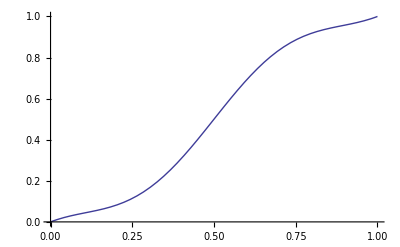

```mathematica
Plot[f408[x],{x,0,1}]
```

```mathematica
f421[x_]:=(22x+Sin[53/5]+Sin[106x/5-53/5])/(22+2Sin[53/5])
```

```mathematica
N[f421[x],20]
```

0.049616836075317710997 (-0.92277542161280675875+22. x-1. Sin[10.6-21.2 x])

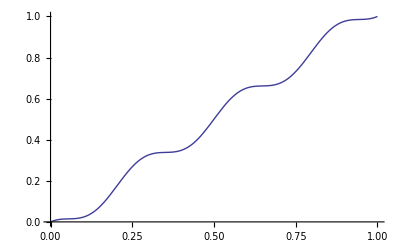

```mathematica
Plot[f421[x],{x,0,1}]
```

```mathematica
N[f421[0]]
```

0.

```mathematica
f423[x_]:=1/2+(53(-11+22x+2Sin[106x/5-53/5]))/(2(Sqrt[8211]+110Pi+55ArcCos[-55/106]))
```

```mathematica
Simplify[N[f423[x],20]]
```

-0.0275182708875260251+1.05503654177505205 x-0.09591241288864109547 Sin[10.6-21.2 x]

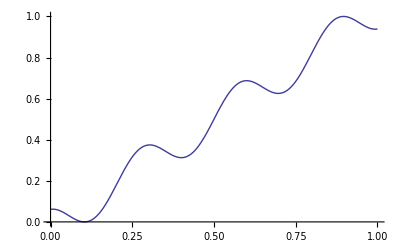

```mathematica
Plot[f423[x],{x,0,1}]
```

```mathematica
piOver2Approx=N[Pi/2,30]
```

1.57079632679489661923132169164

```mathematica
f428[x_]:=1/3(1+x-Sin[9π x+piOver2Approx])
```

```mathematica
Simplify[N[f428[x],20]]
```

0.3333333333333333333+0.33333333333333333333 x-0.3333333333333333333 Sin[1.5707963267948966192+28.274333882308139146 x]

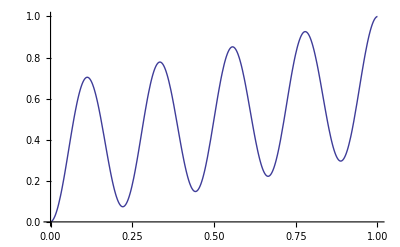

```mathematica
Plot[f428[x],{x,0,1}]
```

```mathematica
N[Maximize[{f428[x],0≤x≤1},{x}]]
```

{0.926134,{x→0.779029}}

```mathematica
f431[x_]:=1/(7Pi+2(Sqrt[100Pi^2]+ArcSec[10Pi]))(Sqrt[100Pi^2-1]+ArcSec[-10Pi]+2Pi(5x-1+5Sin[10Pi x]))
```

```mathematica
Simplify[N[f431[x],20]]
```

0.3039724034453613552+0.3574015604790237888 x+0.3574015604790237888 Sin[31.415926535897932385 x]

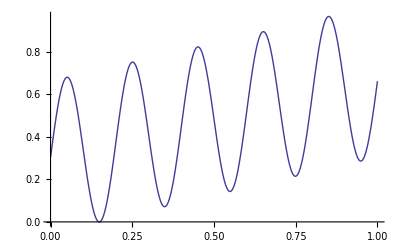

```mathematica
Plot[f431[x],{x,0,1}]
```

```mathematica
Maximize[{N[f431[x]],0≤x≤1},{x}]
```

{0.965346,{x→0.851013}}